# Compound Matrix Method

Implementation of the Compound Matrix Method for solving boundary value eigenvalue problems, as well as a function to generate the linear matrix form from a set of equations.
The first use for a particular dimension stores the coefficients of the matrix in the ODE of the minors, so will take a bit longer.

```mathematica
Needs["CompoundMatrixMethod`"]
```

```mathematica
PacletUninstall["CompoundMatrixMethod"]
SetDirectory["C:\\Users\\mqbssspj\\Dropbox (The University of Manchester)\\Mathematica\\Packages"]
PacletInstall[PackPaclet["CompoundMatrixMethod"]]
```

C:\Users\mqbssspj\Dropbox (The University of Manchester)\Mathematica\Packages

Paclet[CompoundMatrixMethod,0.3,<>]

## Examples

Example 1

Second order ODE: y''(x) + λ^2 y(x) =0, subject to y(0)=y(L)=0. The roots to this can be found analytically to be nπ/L, n ∈ ℤ. 
Converting to the matrix equations, we let y_1=y,y_2=y', then y_1'=y_2,y_2'=-λ^2 y_1 and hence y' =A y, where A=(0 | 1
-λ^2 | 0).
These boundary conditions can be written as matrices as B=C=(1 | 0
0 | 0). 
We can then evaluate the CMM function at values of λ=λ_0, e.g. for λ=1  (with L=3).

```mathematica
CompoundMatrixMethod[{λ,1},{{0,1},{-λ^2,0}},DiagonalMatrix[{1,0}],DiagonalMatrix[{1,0}],{x,0,3}]
```

0.14112

This function be plotted, and is seen to be smooth. Roots of this function correspond to eigenvalues of the original system

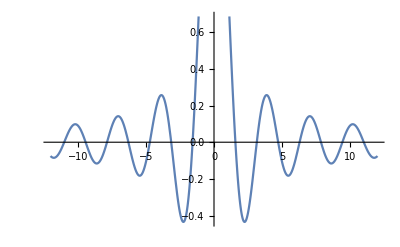

```mathematica
With[{L=2},Plot[CompoundMatrixMethod[{λ,λ0},{{0,1},{-λ^2,0}},DiagonalMatrix[{1,0}],DiagonalMatrix[{1,0}],{x,0,L}],{λ0,-12,12}]]
```

FindRoot will converge to a root:

```mathematica
With[{L=2},FindRoot[CompoundMatrixMethod[{λ,λ0},{{0,1},{-λ^2,0}},DiagonalMatrix[{1,0}],DiagonalMatrix[{1,0}],{x,0,L}],{λ0,2}]]
```

{λ0→1.5708}

We can also use the function ToLinearMatrixForm to convert a system of ODEs into the linearized system directly.

```mathematica
With[{L=2},
sys=ToLinearMatrixForm[y''[x]+λ^2 y[x] ==0,{y[0]==0,y[L]==0},y,{x,0,L}];
Plot[CompoundMatrixMethod[{λ,λ0},sys],{λ0,-12,12}]
]
```

-Graphics-

We could also change the boundary values, e.g. for y(0)+2 y'(0)=0, y'(L)=0

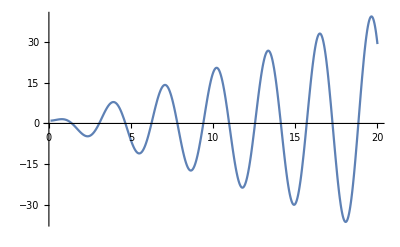

```mathematica
With[{L=2},Plot[CompoundMatrixMethod[{λ,λ0},{{0,1},{-λ^2,0}},{{1,2},{0,0}},DiagonalMatrix[{0,1}],{x,0,L}],{λ0,0.1,20}]]
```

Example 2

This method also works for complex equations , here is y’(x) = ⅈ y(x) + z(x), z'(x)=-λ^2 y(x) + (1-ⅈ)z(x)

```mathematica
example2[λ0_?NumericQ]:=CompoundMatrixMethod[{λ,λ0},{{I,1},{-λ^2,1-I}},DiagonalMatrix[{1,0}],DiagonalMatrix[{1,0}],{x,0,2}]
```

Can find complex roots using FindRoot:

```mathematica
FindRoot[example2[λ0],{λ0,1+I}]
```

{λ0→1.36102-0.367373 ⅈ}

And can plot the real and imaginary parts in the complex plane, intersections of the two curves show roots.

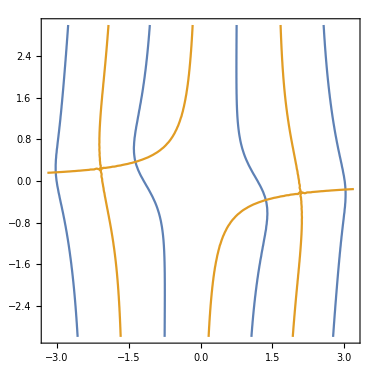

```mathematica
ContourPlot[{Re[example2[λr+I λi]]==0,Im[example2[λr+I λi]]==0},{λr,-3.2,3.2},{λi,-3,3},PlotPoints->30]
```

Example 3

The method also works for odd order equations, for instance y'''- λ^3 y=0, y(0)=y'(0)=0, y(π)=0. 
This equation can be solved using DSolve, and has a range of complex roots

```mathematica
yex3=DSolve[{y'''[x]-λ^3 y[x]==0},y,{x,0,π}][[1]];
cofmat=Table[Coefficient[{y[0]==0,y'[0]==0,y[π]==0}/.yex3/.Equal->Subtract,C[i]],{i,1,3}];
NSolve[{Simplify[Det[cofmat]]==0,-5≤Re@λ≤5,-5≤Im@λ≤5}]//Chop
```

{{λ→-4.81125},{λ→-3.65655},{λ→-2.50185},{λ→-1.34747},{λ→0},{λ→0},{λ→0},{λ→0.673736-1.16694 ⅈ},{λ→0.673736+1.16694 ⅈ},{λ→1.25092-2.16667 ⅈ},{λ→1.25092+2.16667 ⅈ},{λ→1.82828-3.16667 ⅈ},{λ→1.82828+3.16667 ⅈ},{λ→2.40563-4.16667 ⅈ},{λ→2.40563+4.16667 ⅈ}}

ToLinearMatrixForm gives the 3x3 matrix A, and assigns the boundary conditions correctly.

```mathematica
sys3=ToLinearMatrixForm[{y'''[x]-λ^3 y[x]==0},{y[0]==0,y'[0]==0,y[π]==0},y,{x,0,π}]
```

{{{0,1,0},{0,0,1},{λ^3,0,0}},{{{1,0,0},{0,1,0}},{0,0}},{{{1,0,0}},{0}},{x,0,π}}

```mathematica
FindRoot[CompoundMatrixMethod[{λ,λ0},sys3],{λ0,1+I}]//Chop
```

{λ0→0.673736+1.16694 ⅈ}

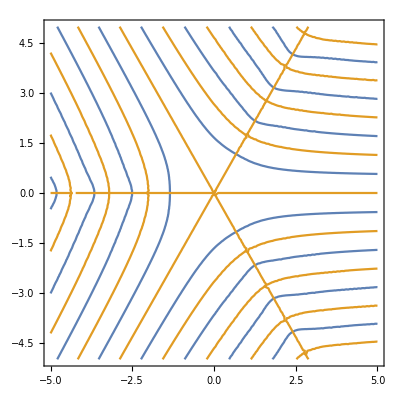

```mathematica
cm3[λ0_?NumericQ]:=CompoundMatrixMethod[{λ,λ0},sys3]
ContourPlot[{Re[cm3[λr+I λi]]==0,Im[cm3[λr+I λi]]==0},{λr,-5,5},{λi,-5,5},PlotPoints->40]
```

Example 4

ϵ^4 y''''(x)+2 ϵ^2 λd/dx[sin(x)dy/dx]+y==0, subject to y (0)==y''(0)==y'(π/2)==y'''(π/2)==0. 
With explicitly giving the matrices:

```mathematica
CompoundMatrixMethod[{λ,1},({{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}, {-1/ϵ^4, (-2λ)/ϵ^2 Cos[x], (-2λ)/ϵ^2 Sin[x], 0}})/.ϵ->1/10,DiagonalMatrix[{1,0,1,0}],DiagonalMatrix[{0,1,0,1}],{x,0,π/2}]
```

-0.650472

Or with the  function to generate the matrix form:

```mathematica
sys=ToLinearMatrixForm[ϵ^4 y''''[x]+2 ϵ^2 λ D[Sin[x]y'[x],x]+y[x]==0,{y[0]==0,y''[0]==0,y'[π/2]==0,y'''[π/2]==0},y,{x,0,π/2}]
```

{{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1/ϵ^4,-(2 λ Cos[x])/ϵ^2,-(2 λ Sin[x])/ϵ^2,0}},{{{1,0,0,0},{0,0,1,0}},{0,0}},{{{0,1,0,0},{0,0,0,1}},{0,0}},{x,0,π/2}}

```mathematica
CompoundMatrixMethod[{λ,1},sys/.ϵ->1/10]
```

-0.650472

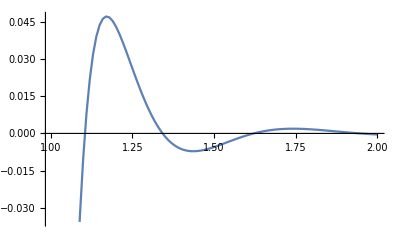

```mathematica
ListLinePlot[Table[{ii,CompoundMatrixMethod[{λ,ii},sys/.ϵ->1/10]},{ii,1,2,0.01}]]
```

```mathematica
FindRoot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->1/10],{λ0,1.1}]
```

{λ0→1.10517}

```mathematica
FindRoot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->1/10],{λ0,1.3}]
```

{λ0→1.34269}

```mathematica
FindRoot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->1/10],{λ0,1.6}]
```

{λ0→1.62184}

```mathematica
FindRoot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->1/10],{λ0,2}]
```

{λ0→1.94586}

The plot of the function is continuous, but there is a sharp turning point around λ=1:

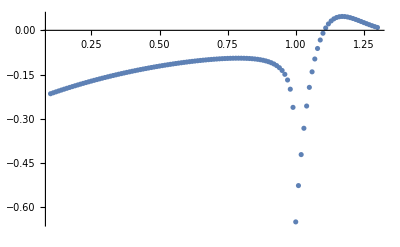

```mathematica
ListPlot[Table[{λ0,CompoundMatrixMethod[{λ,λ0},sys/.ϵ->1/10]},{λ0,0.1,1.3,0.01}],PlotRange->All]
```

Zooming in:

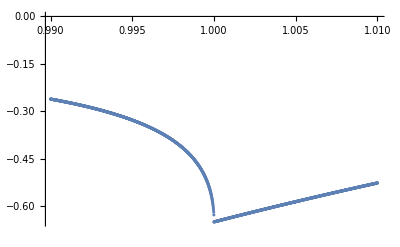

```mathematica
ListPlot[Table[{λ0,CompoundMatrixMethod[{λ,λ0},sys/.ϵ->1/10]},{λ0,0.99,1.01,0.00001}],PlotRange->All]
```

This occurs when the eigenvalues of the matrix A at x=π/2 become entirely imaginary. In general this happens when eigenvalues at either endpoint change type

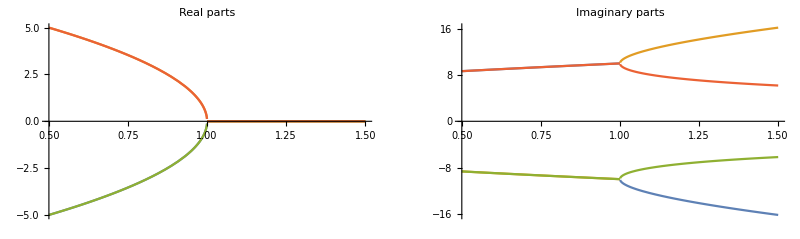

```mathematica
GraphicsRow[{Plot[Evaluate[Re@Eigenvalues[sys[[1]]/.ϵ->1/10/.x->π/2]],{λ,0.5,1.5},PlotLabel->"Real parts"],Plot[Evaluate[Im@Eigenvalues[sys[[1]]/.ϵ->1/10/.x->π/2]],{λ,0.5,1.5},PlotLabel->"Imaginary parts"]},ImageSize->800]
```

Example 5

An example of a 10x10 matrix equation, subject to symmetric boundary conditions at x=0,1.

```mathematica
A2={{0,1,0,0,0,0,5,0,-5,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{-625 ω,-125/2,2,0,0,3,-300,0,300,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,-1.5,0.5,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,-169,0,0,0,0,9175+694 ω,0,811,0},{0,0,0,0,0,0,0,0,0,1},{0,672,0,0,0,0,3222,0,-709+694 ω,0}};
```

Takes a few seconds  for the first evaluation while it builds up the 10 x10 matrix, faster  for the subsequent ones.

```mathematica
CompoundMatrixMethod[{ω,1},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}]//AbsoluteTiming
```

{2.30531,-0.672945}

```mathematica
CompoundMatrixMethod[{ω,1},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}]//AbsoluteTiming
```

{0.596785,-0.672945}

We can see there are a number of positive eigenvalues:

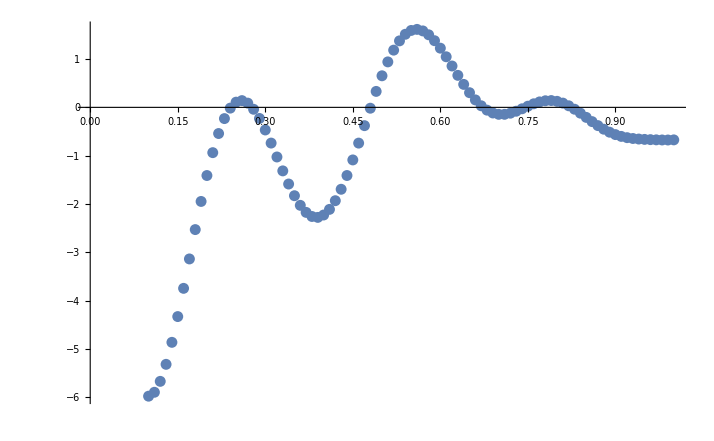

```mathematica
ListPlot[Table[{ωω,CompoundMatrixMethod[{ω,ωω},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}]},{ωω,0.1,1,0.01}]]
```

Example 6

An example with an infinite domain requiring the function w to decay at both ends. 
The equation is (d^4 w)/dx^4-(d^2 w)/dx^2+2(d^2(w w_0))/dx^2+λ w =0, where w_0(x)=3/2 sech^2(x/2), with w decaying at both positive and negative infinity. 

We can get the matrix form by not giving boundary conditions to ToLinearMatrixForm:

```mathematica
A4=ToLinearMatrixForm[w''''[x]-w''[x]+2D[w0[x]w[x],{x,2}]+λ w[x]==0,{},w,x]/.w0->Function[{x},3/2 Sech[x/2]^2]
```

ToLinearMatrixForm::matrixOnly: Incorrect number of boundary conditions given (0 compared to matrix dimension 4), returning the matrix only

{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-λ-2 (-3/4 Sech[x/2]^4+3/2 Sech[x/2]^2 Tanh[x/2]^2),6 Sech[x/2]^2 Tanh[x/2],1-3 Sech[x/2]^2,0}}

These two functions, SelectPositiveEigenvectors (SelectNegativeEigenvectors) are functions to extract the eigenvectors corresponding to positive (negative) eigenvalues at negative (positive) infinity. This requires the eigenvalue to be substituted into the matrix to work.

```mathematica
SelectNegativeEigenvectors[A4/.λ->1,x]//N//Chop
```

{{0.-1. ⅈ,0.5+0.866025 ⅈ,-0.866025-0.5 ⅈ,1.},{0.+1. ⅈ,0.5-0.866025 ⅈ,-0.866025+0.5 ⅈ,1.}}

Set up a function that puts the eigenvalue into the matrix in the boundary value  calculations (and specify a size for the domain L).

```mathematica
example4a[λ0_?NumericQ,L_?NumericQ]:=CompoundMatrixMethod[{λ,λ0},A4,SelectNegativeEigenvectors[A4/.λ->λ0,x],SelectPositiveEigenvectors[A4/.λ->λ0,x],{x,-L,L}]
```

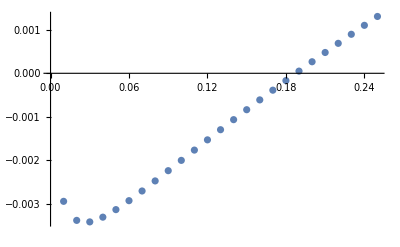

```mathematica
ListPlot[Table[{λ0,example4a[λ0,10]},{λ0,0.01,0.25,0.01}]]
```

Varying the position at which the end point “infinity” conditions are applied at converges to the root (λ_0=3/8):

```mathematica
rootposa=Table[{L,λ0}/.FindRoot[example4a[λ0,L],{λ0,0.2}],{L,3,30}];
```

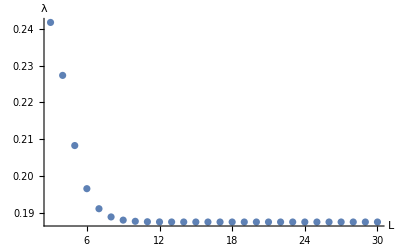

```mathematica
ListPlot[rootposa,PlotRange->All,AxesLabel->{"L","λ"}]
```

Alternatively, we can solve the same equation but use the fact it is an even function to split at zero (so w'(0)=w'''(0)=0).

```mathematica
example4b[λ0_?NumericQ,L_?NumericQ]:=CompoundMatrixMethod[{λ,λ0},A4,DiagonalMatrix[{0,1,0,1}],SelectPositiveEigenvectors[A4/.λ->λ0,x],{x,0,L}]
```

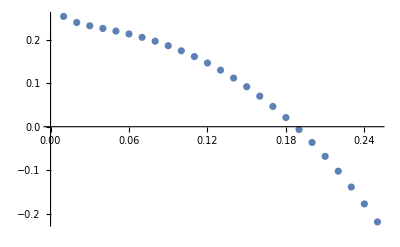

```mathematica
ListPlot[Table[{λ0,example4b[λ0,10]},{λ0,0.01,0.25,0.01}]]
```

```mathematica
rootposb=Table[{L,λ0}/.FindRoot[example4b[λ0,L],{λ0,0.2}],{L,3,30}];
```

Position of the roots are identical for the two methods of solution:

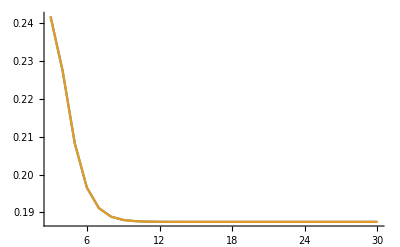

```mathematica
ListLinePlot[{rootposa,rootposb},PlotRange->All]
```

Even if the two functions give different outputs, their roots are in the same place (note the scale change required for the second one)

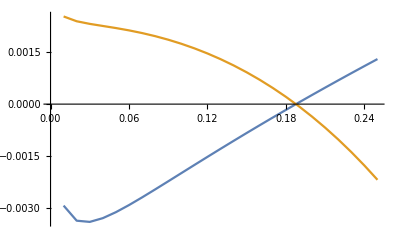

```mathematica
ListLinePlot[{Table[{λ0,example4a[λ0,10]},{λ0,0.01,0.25,0.01}],Table[{λ0,example4b[λ0,10]/100},{λ0,0.01,0.25,0.01}]},Joined->True]
```

Example 7

Linear stability equations for cylinder rotating inside another, [ϵ^2 ∂_yy - 1]^2u(y) = ϵ^2 T V(y) v(y),  [ϵ^2 ∂_yy -1] v(y) = ϵ^2 T u(y) V' (y), ϵ u'(y) + I w(y) =0, where V(y) = 1-y.

Set up the equations, note that the equation for w does not contain any derivatives, but the code handles that appropriately.

```mathematica
dd=(ϵ^2 D[#,{y,2}]-#)&;
sys=ToLinearMatrixForm[{dd[dd[u[y]]]==ϵ^2 T V[y]v[y],dd[v[y]]==ϵ^2 u[y]V'[y],ϵ u'[y]+ I w[y]==0},{u[0]==0,v[0]==0,w[0]==0,u[1]==0,v[1]==0,w[1]==0},{u,v,w},{y,0,1}]
```

{{{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{-1/ϵ^4,0,2/ϵ^2,0,(T V[y])/ϵ^2,0},{0,0,0,0,0,1},{V'[y],0,0,0,1/ϵ^2,0}},{{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,ⅈ ϵ,0,0,0,0}},{0,0,0}},{{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,ⅈ ϵ,0,0,0,0}},{0,0,0}},{y,0,1}}

Define a function to calculate the CMM function for a given ϵ and T:

```mathematica
Clear[tempfn];
tempfn[ee_?NumericQ,TT_?NumericQ]:=CompoundMatrixMethod[{T,TT},sys/.V->Function[{y},1-y]/.ϵ->ee]
```

Find a value of T for ϵ = 0.1:

```mathematica
CompoundMatrixMethod[{T,1},(sys/.V->Function[{y},1-y]/.ϵ->0.1)]
```

-3.1251×10^-7+6.93944×10^-27 ⅈ

```mathematica
FindRoot[tempfn[1/10,t],{t,20000}]
```

{t→26242.5}

Loop through varying ϵ to construct sections of a neutral curve. Start at the previous value to stay along the same curve (takes a while to follow the roots)

```mathematica
lastroot={TT->26242};
etab=Monitor[Table[lastroot=FindRoot[tempfn[e,TT],{TT,TT/.lastroot},DampingFactor->0.2];{e,TT}/.lastroot,{e,0.1,1,0.1}],e];//Quiet
```

```mathematica
lastroot={TT->26242};
etab2=Monitor[Table[lastroot=FindRoot[tempfn[e,TT],{TT,1.4*TT/.lastroot},DampingFactor->0.2];{e,TT}/.lastroot,{e,Reverse@Range[0.03,0.1,0.005]}],e];//Quiet
```

Plot the neutral curve:

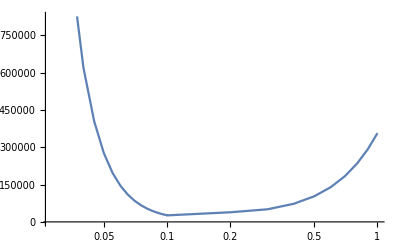

```mathematica
ListLogLinearPlot[Sort@(Join@@{etab,etab2}),Joined->True]
```

There is another neutral curve at higher values of T:

```mathematica
lastroot={T->226242};
etab4=Monitor[Table[lastroot=FindRoot[tempfn[e,T],{T,T/.lastroot},DampingFactor->0.2];{e,T}/.lastroot,{e,0.1,1,0.1}],e]
```

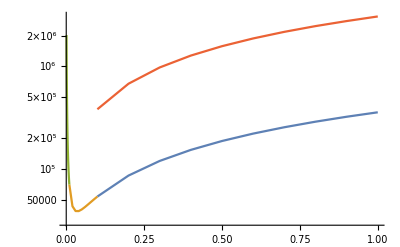

```mathematica
ListLogPlot[{etab,etab2,etab3,etab4},Joined->True,PlotRange->All]
```

These additional roots for a given value of T can seen:

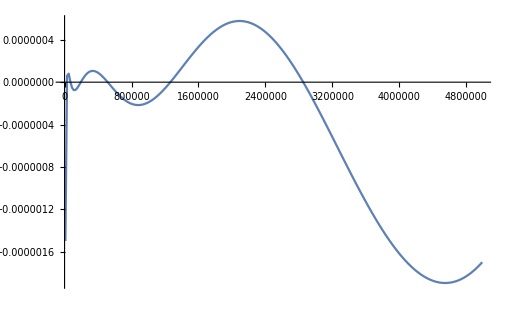

```mathematica
Table[{tt,tempfn[0.1,tt]},{tt,10^4,5*10^6,2*10^4}]//ListLinePlot
```